# Getting Started with Mathematica

Calvin Sprouse
2024 March 03
PHYS 361

## Defining a variable

```mathematica
a=1;
```

## Defining a function

```mathematica
f[x_]:=x^a-2;
```

## Simplifying a long algebraic expression

```mathematica
g[θ_]:=E^(I*θ)-E^(-I*θ)+(Cos[2]-I*Sin[2]);
FullSimplify[g[θ]]
```

ⅇ^(-ⅈ Conjugate[θ])-ⅇ^(ⅈ Conjugate[θ])+Cos[2]+ⅈ Sin[2]

ⅇ^(-2 ⅈ)+2 ⅈ Sin[θ]

## Solve an algebraic expression

```mathematica
Solve[g[θ]==E^(-2*I),θ, Assumptions->{θ∈Integers}]
```

{{θ→0}}

## Plot a function

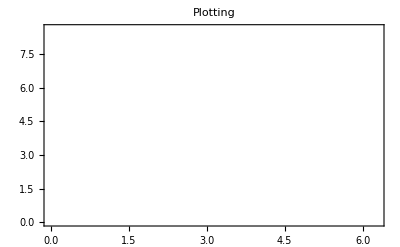

```mathematica
Plot[
Abs[g[θ]]^2,
{θ,0,2π},
Frame->True,
PlotLabel->"Plotting ",
FrameLabel->{"",""},
LabelStyle->{FontSize->12,FontFamily->"Times New Roman",FontColor->White},
PlotStyle->White]
```

## Solve a definite integral

```mathematica
j[x_]=E^x*Sin[2*x];
∫_0^1 j[x]ⅆx
```

1/5 (2-2 ⅇ Cos[2]+ⅇ Sin[2])

## Solve an indefinite integral

```mathematica
∫j[x]ⅆx
```

1/5 ⅇ^x (-2 Cos[2 x]+Sin[2 x])